# Reviewing Probability

We will discuss the concept of probability and how it relates to the frequency of different outcomes in a repeatable measurement. Then we will show how probabilities in quantum theory help us calculate joint and marginal probabilities.

## Key Concepts

Random outcome

Probability distribution

Marginal probability

Joint probability

## Frequency vs probability

You’re no doubt familiar with coin flips or dice rolls as ways to generate random outcomes. For our purposes, think of a random outcome as a definite result from a repeatable experiment. Randomness here means that several different outcomes are possible, and while we may know their probabilities, there is no way to determine which specific outcome will occur before running the experiment.

You can find much more information on probability and statistics in any of the following Wolfram U courses: Introduction to Probability, and Introduction to Statistics.

Quantum theory provides a way to compute the probability distribution over possible measurement outcomes. You can think of a probability distribution as a rule that assigns a nonnegative probability to each possible outcome of an experiment, with all probabilities adding up to 1. In quantum circuits, this distribution is typically defined over the discrete set of possible bitstrings.

Let’s look at a couple examples of generating random outcomes to build intuition.

Suppose you want to sample a random integer between 1 and 10. One realization of this process is as follows:

```mathematica
RandomInteger[{1,10}]
```

2

The above function returns a uniformly random integer from 1 to 10 (inclusive).

Now examine the count of each number in the sequence above.

```mathematica
numberdata=RandomInteger[{1,10},50]
```

{6,4,9,9,10,3,8,7,2,1,3,3,7,5,6,8,10,10,10,8,8,6,8,8,10,1,4,7,2,2,8,3,2,7,1,4,2,9,7,7,4,4,8,3,7,8,10,7,4,8}

Now examine the frequency of each number in the sequence above:

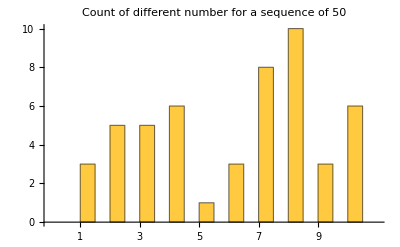

```mathematica
Histogram[numberdata,]
```

Now examine the frequency of each number across different sequences as the sequence length increases:

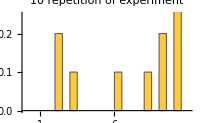
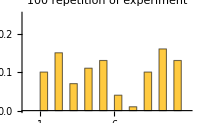
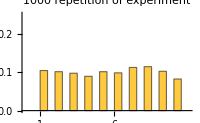
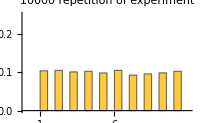
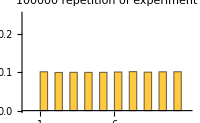

```mathematica
Row[Table[Histogram[RandomInteger[{1,10},j],],{j,10^Range[5]}]]
```

As you can see, with more repetition of the same experiment, the observed frequency of outcomes gets closer to the true probability distribution.

Now let’s consider the case where we assign a specific weight to each number: {1,1,2,3,4,4,3,2,1,1}.
We can compute the corresponding probabilities by normalizing the weights; that is:

```mathematica
probWeights=Normalize[{1,1,2,3,4,4,3,2,1,1},Total]
```

{1/22,1/22,1/11,3/22,2/11,2/11,3/22,1/11,1/22,1/22}

If we run the experiment many times, we expect the frequency of results to converge to the probabilities above. Now let’s generate different data samples of results for 10, 100, and 10,000 runs. As the number of realizations increases, the observed frequencies should get closer to the expected probabilities.

```mathematica
sequenceOfResults=Table[RandomChoice[{1,1,2,3,4,4,3,2,1,1}->Range[10],j],{j,2^{6,8,10}}];
```

Calculate frequencies for each experiment:

```mathematica
freq=KeySort[Join[AssociationThread[Range[10]->0],Normalize[Counts[#],Total]]]&/@sequenceOfResults
```

{<|1→1/16,2→1/64,3→5/64,4→3/16,5→1/4,6→11/64,7→5/64,8→9/64,9→1/64,10→0|>,<|1→7/128,2→13/256,3→1/16,4→3/32,5→53/256,6→47/256,7→39/256,8→7/64,9→5/128,10→3/64|>,<|1→43/1024,2→23/512,3→53/512,4→33/256,5→11/64,6→193/1024,7→133/1024,8→105/1024,9→25/512,10→5/128|>}

Visualize the results:

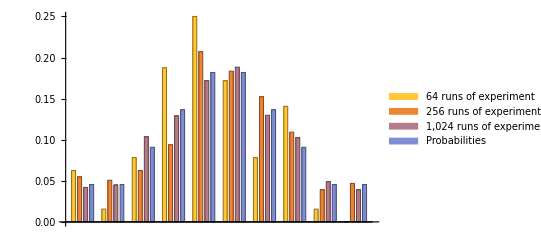

```mathematica
BarChart[Transpose@Append[Values/@freq,probWeights],ChartLegends->{"64 runs of experiment","256 runs of experiment","1,024 runs of experiment","Probabilities"}]
```

As expected, with more runs of the experiment, the observed frequencies get closer to the expected probabilities (law of large numbers).

Now let’s consider a case analogous to three different players rolling dice and collecting their joint outcomes. Of course, the quantum case can differ markedly from the classical one—classically, similar correlations might require prearranged strategies or communication. For the moment, however, we will set aside interpretation and focus only on the probabilities of the outcomes (i.e., the joint distribution and any marginals), leaving the discussion of correlations for later.

## Joint vs marginal probabilities

Consider a three-qubit system. Each qubit is measured in the computational basis, so any measurement result can be described by a three-bit string; overall 2^3 possible outcomes:

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

We will prepare the system in a special initial state. For now, we will skip the details of what this state is and focus only on the probability of outcomes. Using quantum theory, we can calculate the joint probabilities of the measurement results, that is, the probabilities for all possible tuples of 0s and 1s listed above.

```mathematica
state=QuantumState["RandomPure"[3]];
state["Probabilities"]
```

<|000→0.380373,001→0.0599693,010→0.0143558,011→0.0909716,100→0.267792,101→0.0244699,110→0.0204081,111→0.141661|>

Generate the corresponding multivariate distribution of outcomes:

```mathematica
𝒟=QuantumMeasurementOperator[{{1},{2},{3}}][state]["MultivariateDistribution"];
```

Visualize the contingency table of the distribution:

```mathematica
Information[𝒟,"ProbabilityTable"]
```

Since we have the multivariate distribution, we can compute the probability of any scenario by summing over the appropriate outcomes. Let’s consider a few cases.

Calculate the probability of getting 0 for qubit-1 and 1 for qubit-3 (and any result for qubit-2)

```mathematica
Probability[q1==0&&q3==1,{q1,q2,q3}\[Distributed]𝒟]
```

0.150941

Let’s calculate the above probability step-by-step:
- From the full list of outcome–probability pairs, select the outcomes whose first bit is 0 and last bit is 1 (i.e., {0,b,1} with be can be either 0 or 1, but we do not care).
- Extract the probabilities associated with those selected outcomes.
- Add those probabilities together.

We can use the multivariate distribution and compute the full list of outcome–probability pairs:

```mathematica
prob={#,PDF[𝒟,#]}&/@Tuples[{0,1},3];
TableForm[prob,]
```

Outcome | Probability
{0,0,0} | 0.380373
{0,0,1} | 0.0599693
{0,1,0} | 0.0143558
{0,1,1} | 0.0909716
{1,0,0} | 0.267792
{1,0,1} | 0.0244699
{1,1,0} | 0.0204081
{1,1,1} | 0.141661

```mathematica
Total@Select[prob,#[[1,1]]==0&&#[[1,3]]==1&][[All,-1]]
```

0.150941

Now suppose we do not care about qubit 3 and want to focus only on the statistics of qubits 1 and 2. To do this, we compute the marginal distribution by summing over the outcomes of qubit 3. (In the quantum formalism, this corresponds to taking the partial trace over qubit 3 to obtain the reduced state of qubits 1 and 2.)

To get the marginal distribution, the calculation as follows:
- first group outcomes based on the values of the first and second elements (we are only interested in the marginal distribution qubit 1 and 2)
- for each group, add up the values of probabilities

```mathematica
GroupBy[prob,(#[[1]][[;;2]]&)->Last,Total]
```

<|{0,0}→0.440342,{0,1}→0.105327,{1,0}→0.292262,{1,1}→0.162069|>

The same process can be done more cleanly using built-in Wolfram Language functionality. This makes it much easier to compute other probabilities as well (you’ll see this shortly).

Calculate  the marginal distribution

```mathematica
𝒟12=MarginalDistribution[𝒟,{1,2}]
```

CategoricalDistribution[…]

Visualize the contingency table of the marginal distribution:

```mathematica
Information[𝒟12,"ProbabilityTable"]
```

Calculate the probability of getting 0 for qubit-1 from the marginal probability distribution:

```mathematica
Probability[q1==0,{q1,q2}\[Distributed]𝒟12]
```

0.545669

Calculate the probability of getting 0 for qubit-1 from the overall probability distribution:

```mathematica
Probability[q1==0,{q1,q2,q3}\[Distributed]𝒟]
```

0.545669

Of course, the rules of quantum theory provide a recipe for obtaining the quantum state of qubits 1 and 2 by averaging over all contributions from qubit 3. This is done by tracing over the degrees of freedom of qubit 3, which yields the reduced state for qubits 1 and 2.

Trace out the qubit-3 (which is the 3rd subsystem) from the overall state:

```mathematica
QuantumPartialTrace[state,{3}]
```

QuantumState[…]

And this reduced state yields the same marginal probabilities as before:

```mathematica
QuantumPartialTrace[state,{3}]["Probabilities"]
```

<|00→0.440342,01→0.105327,10→0.292262,11→0.162069|>

```mathematica
Information[𝒟12,"Probabilities"]
```

<|{0,0}→0.440342,{0,1}→0.105327,{1,0}→0.292262,{1,1}→0.162069|>

In future chapters, we will discuss in details the idea of tracing out a subsystem and how to describe the state of composite systems in quantum theory.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]